# VYA - Přednášky

## 8. Přednáška

### Komplexní čísla

```mathematica
Quiet[Remove["Global`*"]];
```

```mathematica
z = 3 + 4I
```

3+4 ⅈ

```mathematica
?I
```

```mathematica
{z, Re[z], Im[z], Abs[z], √(Re[z]^2+ Im[z]^2), Arg[z]}
```

{3+4 ⅈ,3,4,5,5,ArcTan[4/3]}

```mathematica
Arg /@ {0, I, -1, -I}
```

{0,π/2,π,-π/2}

```mathematica
?Arg
```

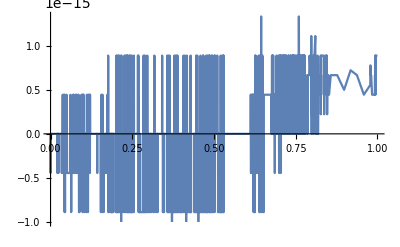

```mathematica
U1[t_] := 5*Sin[3t + 0.4]
U2[t_] := Im[5 * Exp[I * 0.4] * Exp[I * 3 * t]]
Plot[U1[t] - U2[t], {t, 0, 1}]
```

```mathematica
Sin[psi + Pi/2]
```

Cos[psi]

```mathematica
Sin'
```

Cos[#1]&

```mathematica
{Abs[I], Arg[I]}
```

{1,π/2}

### Chování RLC v HUS

R: u_R(t) = R*I_R(t) 
	U_R = R*I_R
L: u_L(t) = L*dI_L/dt
	U_L = L*j*ω*I
C: I_c(t) = C*dU_c/dt
	I_C = C*j*ω*U_C
U_C = 1/(j*ω*C)*I_C